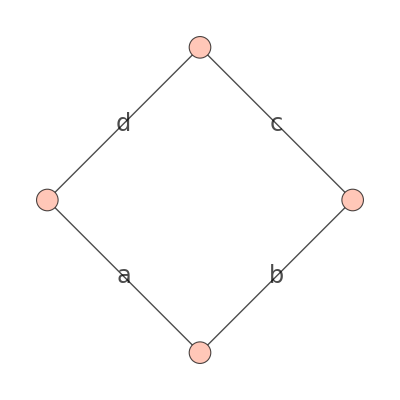

```mathematica
g=AdjacencyGraph[{{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0}},EdgeLabels->{1<->2->Style["a",FontSize->24],2<->3->Style["b",FontSize->24],3<->4->Style["c",FontSize->24],4<->1->Style["d",FontSize->24]},VertexLabels->Placed["Name",Center],EdgeStyle->Black,VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]]
```

```mathematica
IncidenceMatrix[g]//MatrixForm
```

(1 | 1 | 0 | 0
1 | 0 | 1 | 0
0 | 0 | 1 | 1
0 | 1 | 0 | 1)

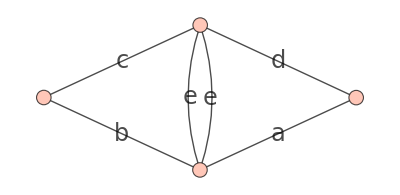

(1 | 1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 1 | 1)

```mathematica
g=AdjacencyGraph[{{0,1,0,1},{1,0,1,2},{0,1,0,1},{1,2,1,0}},EdgeLabels->{1<->2->Style["a",FontSize->24],2<->3->Style["b",FontSize->24],3<->4->Style["c",FontSize->24],4<->1->Style["d",FontSize->24],4<-> 2->Style["e",FontSize->24]},VertexLabels->Placed["Name",Center],EdgeStyle->Black,VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]]
IncidenceMatrix[g]//MatrixForm
```

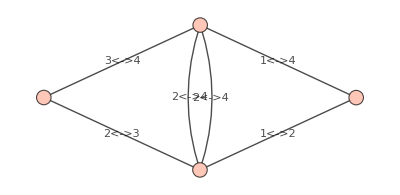

(1 | 1 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 1 | 1)

```mathematica
g=AdjacencyGraph[{{0,1,0,1},{1,0,1,2},{0,1,0,1},{1,2,1,0}},EdgeLabels->"Name",VertexLabels->Placed["Name",Center],EdgeStyle->Black,VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]]
IncidenceMatrix[g]//MatrixForm
```

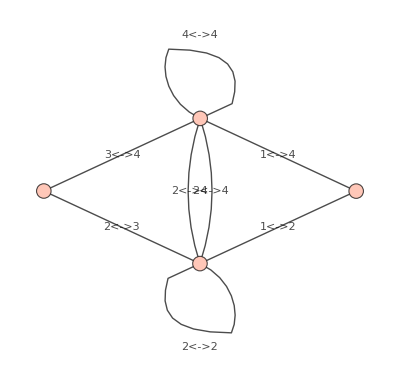

(1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 2 | 1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 1 | 1 | 1 | 2)

```mathematica
g=AdjacencyGraph[{{0,1,0,1},{1,1,1,2},{0,1,0,1},{1,2,1,1}},EdgeLabels->"Name",VertexLabels->Placed["Name",Center],EdgeStyle->Black,VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]]
IncidenceMatrix[g]//MatrixForm
```

```mathematica
g=AdjacencyGraph[{{0,1,0,1},{1,0,1,0},{0,1,0,1},{1,0,1,0}},EdgeStyle->{Red,Thick},VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]]
```

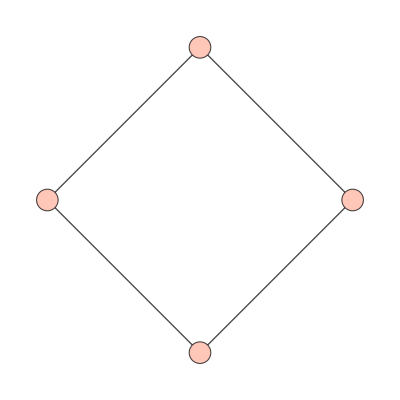

Set::write: Tag Inherited in Inherited[State] is Protected.

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
g=AdjacencyGraph[{{0,1,0,1},{1,0,1,2},{0,1,0,1},{1,2,1,0}},EdgeStyle->{Red,Thick},VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]]
```

Set::write: Tag Inherited in Inherited[State] is Protected.

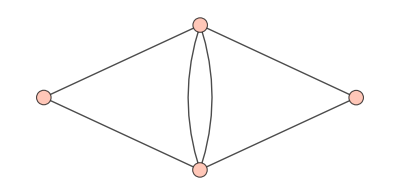

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
g=AdjacencyGraph[{{0,1,0,1},{1,1,1,2},{0,1,0,1},{1,2,1,1}},EdgeStyle->Thick,VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]]
```

Set::write: Tag Inherited in Inherited[State] is Protected.

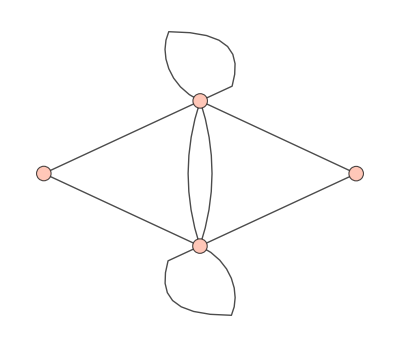

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
AdjacencyGraph[{{1,1,1,1},{1,0,3,1},{1,3,0,2},{1,1,2,0}},EdgeStyle->Thick,VertexSize->Small,VertexStyle->RGBColor[1,.78,.72]]
```

```mathematica
AdjacencyGraph[{{0,1,1,3},{1,0,1,2},{1,1,1,1},{3,2,1,0}},EdgeStyle->Thick,VertexSize->Small,VertexStyle->RGBColor[1,.78,.72],GraphLayout->"CircularEmbedding"]
```

Set::write: Tag Inherited in Inherited[State] is Protected.

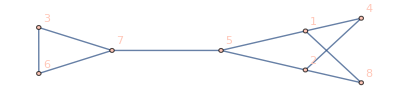

```mathematica
g=RandomGraph[{8,10},EdgeStyle->{Red,Thick},VertexSize->Small,VertexStyle->RGBColor[1,.78,.72],VertexLabels->Automatic]
```

```mathematica
FindShortestPath[g,3,8]
HighlightGraph[g,PathGraph[%],VertexLabels->Automatic]
```

{3,7,5,1,8}

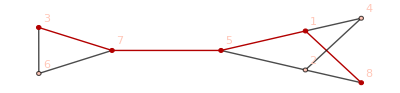

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
GraphData["Regular",4]
```

{{Empty,4},{LadderRung,2},SquareGraph,TetrahedralGraph}

```mathematica
GraphData["TetrahedralGraph"]
```

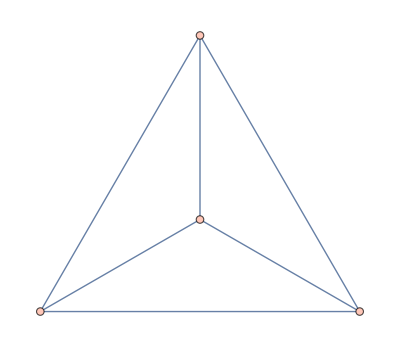

Set::write: Tag Inherited in Inherited[State] is Protected.

{{Empty,3},TriangleGraph}

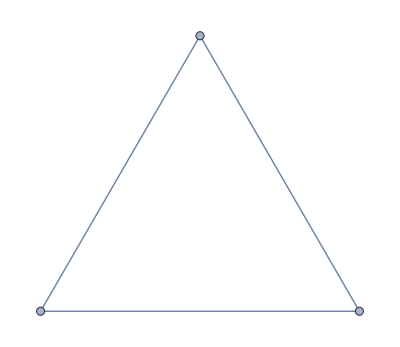

```mathematica
GraphData["Regular",3]
GraphData["TriangleGraph"]
```

{{Cycle,5},{Empty,5},PentatopeGraph}

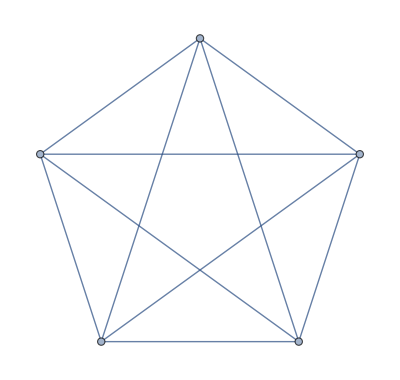

```mathematica
GraphData["Regular",5]
GraphData["PentatopeGraph"]
```

```mathematica
GraphData["Regular",6]
GraphData["OctahedralGraph"]
```

{2C3,{Complete,6},{Cycle,6},{Empty,6},{LadderRung,3},OctahedralGraph,{Prism,3},UtilityGraph}

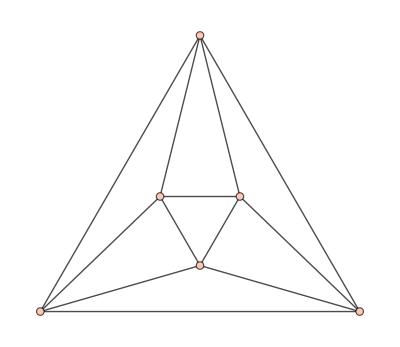

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
GraphData["Regular",8]
GraphData["WagnerGraph"]
```

{2C4,2K4,{Antiprism,4},C5+C3,{Circulant,{8,{1,2,4}}},{Circulant,{8,{1,3,4}}},{Complete,8},{CompleteBipartite,{4,4}},{Cone,{5,3}},{Cubic,{8,2}},{Cubic,{8,3}},CubicalGraph,{Cycle,8},{Empty,8},{LadderRung,4},{MinimalRegularMatchstick,3},{Quartic,{8,1}},{Quartic,{8,4}},{Quartic,{8,5}},{Rook,{2,4}},SixteenCellGraph,WagnerGraph}

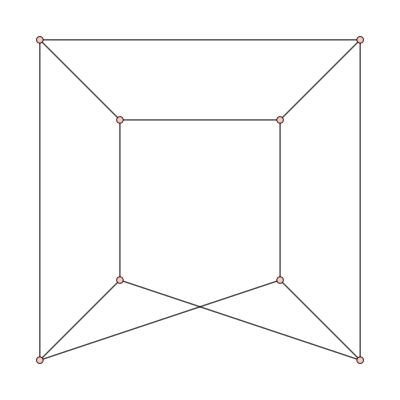

Set::write: Tag Inherited in Inherited[State] is Protected.

{{Empty,4},{LadderRung,2},SquareGraph,TetrahedralGraph}

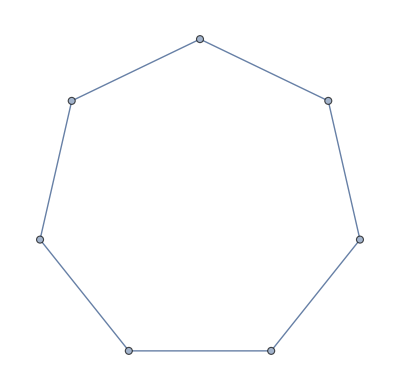

```mathematica
GraphData["Regular",4]
GraphData[{"Cycle", 7}]
```

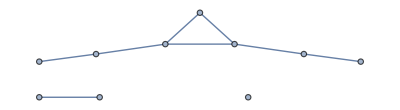

False

```mathematica
RandomGraph[{10,8}]
ConnectedGraphQ[%]
```

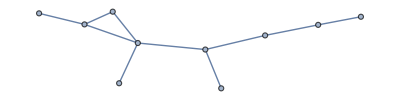

True

```mathematica
RandomGraph[{10,10}]
ConnectedGraphQ[%]
```

```mathematica
Graph[-Graphics-,EdgeStyle->{Red,Thick},VertexStyle->RGBColor[1,.78,.72]]
```

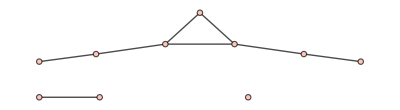

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[-Graphics-,EdgeStyle->{Red,Thick},VertexStyle->RGBColor[1,.78,.72]]
```

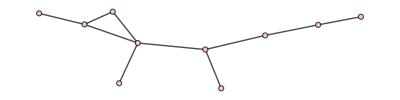

Set::write: Tag Inherited in Inherited[State] is Protected.

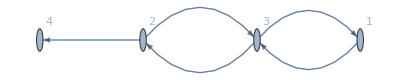

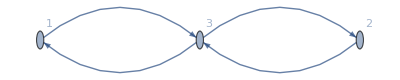

```mathematica
RandomGraph[{4,5},DirectedEdges->True,VertexLabels->Automatic]
Subgraph[%,{1,2,3}]
```

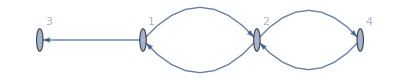

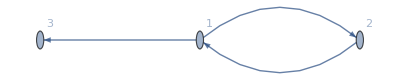

```mathematica
RandomGraph[{4,5},DirectedEdges->True,VertexLabels->Automatic]
Subgraph[%,{1,2,3}]
```

```mathematica
Graph[-Graphics-,EdgeStyle->Thick,VertexSize->Small,VertexStyle->RGBColor[1,.78,.72],VertexLabels->None]
```

```mathematica
Graph[-Graphics-,EdgeStyle->Thick,VertexSize->Small,VertexStyle->RGBColor[1,.78,.72],VertexLabels->None]
```

```mathematica
g=RandomGraph[{5,8},DirectedEdges->True,EdgeStyle->Thick,VertexSize->Small,VertexStyle->RGBColor[1,.78,.72],VertexLabels->None]
```

```mathematica
Graph[g,GraphLayout->"LinearEmbedding"]
Graph[g,VertexLabels->Automatic]
Graph[g,GraphLayout->"LinearEmbedding",VertexLabels->Automatic]
```

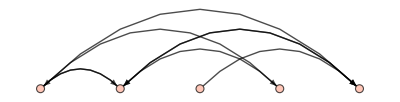

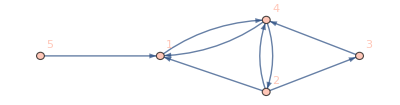

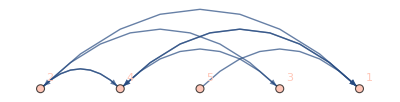

```mathematica
g=RandomGraph[{5,8},DirectedEdges->True,EdgeStyle->Thick,VertexSize->Small,VertexStyle->RGBColor[1,.78,.72],VertexLabels->None]
AdjacencyMatrix[g]//MatrixForm
Graph[g,VertexLabels->Automatic]
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
-1 | -1 | -1 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | -1 | -1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | -1 | -1 | 0
0 | 0 | 1 | 0 | 1 | 0 | 1 | -1)

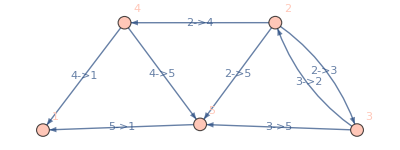

```mathematica
IncidenceMatrix[g]//MatrixForm
Graph[g,VertexLabels->Automatic,EdgeLabels->"Name"]
```

```mathematica
EdgeList[-Graphics-]
```

{2->3,2->4,2->5,3->2,3->5,4->1,4->5,5->1}

(0 | 0 | 0 | 0 | 0 | -1 | 0 | -1
1 | 1 | 1 | -1 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | -1 | 0 | -1 | 0 | -1 | 1)

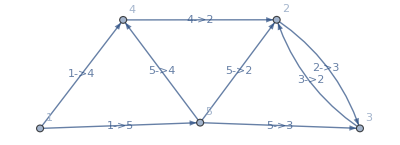

```mathematica
{-{0,0,0,0,0,1,0,1},-{-1,-1,-1,1,0,0,0,0},-{1,0,0,-1,-1,0,0,0},-{0,1,0,0,0,-1,-1,0},-{0,0,1,0,1,0,1,-1}}//MatrixForm
IncidenceGraph[%,VertexLabels->Automatic,EdgeLabels->"Name"]
```

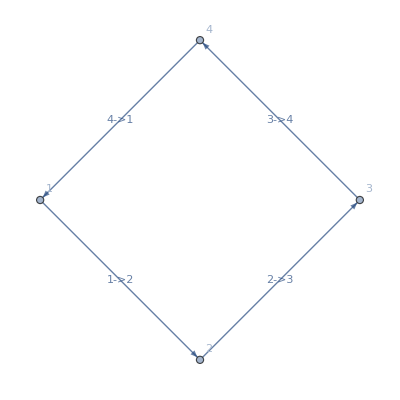

(-1 | 0 | 0 | 1
1 | -1 | 0 | 0
0 | 1 | -1 | 0
0 | 0 | 1 | -1)

{1->2,2->3,3->4,4->1}

```mathematica
h=Graph[{1->2,2->3,3->4,4->1},VertexLabels->"Name",EdgeLabels->"Name"]
IncidenceMatrix[h]//MatrixForm
EdgeList[h]
```

(0 | 1 | 1 | 1
1 | 0 | 1 | 0
1 | 1 | 0 | 0
0 | 0 | 1 | 0)

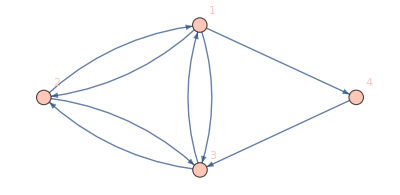

```mathematica
g=RandomGraph[{4,8},DirectedEdges->True,EdgeStyle->Thick,VertexSize->Small,VertexStyle->RGBColor[1,.78,.72],VertexLabels->None]
AdjacencyMatrix[g]//MatrixForm
Graph[g,VertexLabels->Automatic]
```

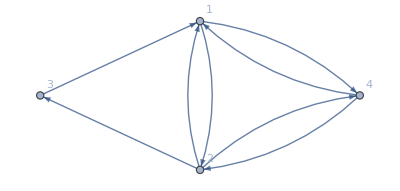

```mathematica
AdjacencyGraph[{{0,1,0,1},{1,0,1,1},{1,0,0,0},{1,1,0,0}},VertexLabels->Automatic]
```

```mathematica
IsomorphicGraphQ[-Graphics-,-Graphics-]
```

True

```mathematica
AdjacencyGraph[{{1,0},{0,1}},EdgeStyle->{Red,Thick},VertexSize->Small,VertexStyle->RGBColor[1,.78,.72],DirectedEdges->True]
```

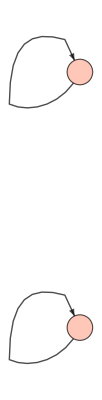

```mathematica
AdjacencyGraph[{{0,1},{1,0}},EdgeStyle->{Red,Thick},VertexSize->Small,VertexStyle->RGBColor[1,.78,.72],DirectedEdges->True]
```

```mathematica
AdjacencyGraph[{{0,0},{1,1}},EdgeStyle->{Red,Thick},VertexSize->Small,VertexStyle->RGBColor[1,.78,.72],DirectedEdges->True]
```